```mathematica
data=Flatten@Import["C:\\Users\\Sebastian\\Dropbox\\Studie\\Kurser\\Datalogi\\PCSD\\Assignments\\1\\tex\\lots-of-clients_100reqs_zipf0.5.txt","TSV"]
```

{== 1 simultaneous workers ==,1205,== 4 simultaneous workers ==,719,757,799,853,== 7 simultaneous workers ==,1072,1102,1173,1143,1137,1252,622,== 10 simultaneous workers ==,1217,1354,1525,1400,1526,1657,1095,1201,1071,785,== 13 simultaneous workers ==,866,919,908,987,910,914,1013,1042,921,1018,1119,1145,691,== 16 simultaneous workers ==,2558,2623,2621,2643,2634,2661,2690,2645,2660,2674,2677,2673,1732,1724,1716,1724,== 19 simultaneous workers ==,2630,2643,2671,2681,2688,2721,2678,2713,2679,2704,2683,2721,2658,2683,2660,2654,2636,2648,568,== 22 simultaneous workers ==,1435,1449,1488,1297,1313,1302,1254,1254,1265,1274,1305,1301,1344,1317,1311,1355,1381,1369,1425,1491,1463,673,== 25 simultaneous workers ==,4117,4176,4182,4195,4255,4243,4291,4329,4367,4259,4298,4416,4343,4511,4339,4389,4541,4479,3518,3509,3423,3396,3360,3457,3505,== DONE ==}

```mathematica
fancyData=Nest[
Module[{
nums=TakeWhile[#[[1,2;;]],IntegerQ]
},{
#[[1,(2+Length@nums);;]],
Append[#[[2]],nums]
}]&,{data,{}},25][[2]]
```

{{1205},{719,757,799,853},{1072,1102,1173,1143,1137,1252,622},{1217,1354,1525,1400,1526,1657,1095,1201,1071,785},{866,919,908,987,910,914,1013,1042,921,1018,1119,1145,691},{2558,2623,2621,2643,2634,2661,2690,2645,2660,2674,2677,2673,1732,1724,1716,1724},{2630,2643,2671,2681,2688,2721,2678,2713,2679,2704,2683,2721,2658,2683,2660,2654,2636,2648,568},{1435,1449,1488,1297,1313,1302,1254,1254,1265,1274,1305,1301,1344,1317,1311,1355,1381,1369,1425,1491,1463,673},{4117,4176,4182,4195,4255,4243,4291,4329,4367,4259,4298,4416,4343,4511,4339,4389,4541,4479,3518,3509,3423,3396,3360,3457,3505}}

```mathematica
latencyData={Length[#],Total[#]/(100*Length[#])}&/@fancyData//N
```

{{1.,12.05},{4.,7.82},{7.,10.7157},{10.,12.831},{13.,9.57923},{16.,24.1594},{19.,25.6416},{22.,13.2118},{25.,40.7592}}

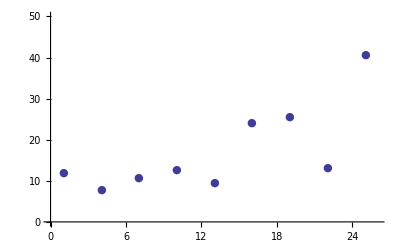

```mathematica
ListPlot[latencyData,PlotRange->{{0,26},{0,50}},PlotMarkers->{Automatic,Small}]
```